```mathematica
Clear[diff];
Clear["Global`*"]
```

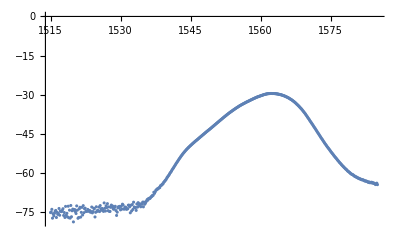

```mathematica
spec=Import["Data.xlsx",Path->NotebookDirectory[]][[1]];
spec=Delete[spec,1];ListPlot[spec]
```

```mathematica
diff={{-1,1},{-1/2,0,1/2},{1/12,-2/3,0,2/3,-1/12}};
yv=spec[[All,2]];
h=spec[[2,1]]-spec[[1,1]];
```

```mathematica
(*первый порядок*)
```

```mathematica
ideg=1;
dy1=ListCorrelate[diff[[ideg]],yv];
dy1=Insert[dy1,yv[[-1]]-yv[[-2]],-1];
dy1=dy1/h;
```

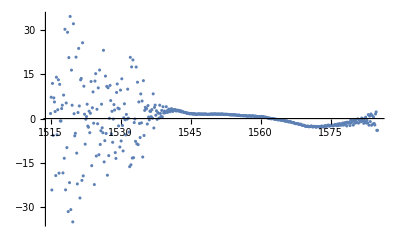

```mathematica
diffspec=spec;
diffspec[[All,2]]=dy1;
ListPlot[diffspec,PlotRange->All]
```

```mathematica
(*Второй порядок*)
```

```mathematica
ideg=2;
dy2=ListCorrelate[diff[[ideg]],yv];
dy2=Insert[dy2,{-3/2,2,-1/2}.yv[[1;;3]],1];
dy2=Insert[dy2,{1/2,-2,3/2}.yv[[-3;;-1]],-1];
dy2=dy2/h;
```

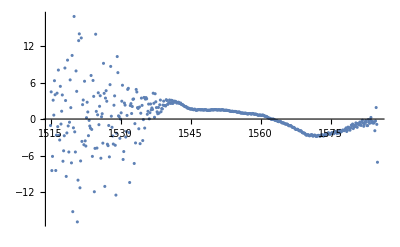

```mathematica
diffspec=spec;
diffspec[[All,2]]=dy2;
ListPlot[diffspec,PlotRange->All]
```

```mathematica
(*Четвертый порядок*)
```

```mathematica
ideg=3;
dy4=ListCorrelate[diff[[ideg]],yv];
dy4=Insert[dy4,{−25/12,4,−3,4/3,-1/4}.yv[[1;;5]],1];
dy4=Insert[dy4,{−25/12,4,−3,4/3,-1/4}.yv[[2;;6]],2];
dy4=Insert[dy4,{1/4,-4/3,3,-4,25/12}.yv[[-5;;-1]],-1];
dy4=Insert[dy4,{1/4,-4/3,3,-4,25/12}.yv[[-6;;-2]],-2];
dy4=dy4/h;
```

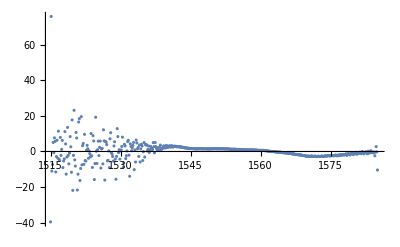

```mathematica
diffspec=spec;
diffspec[[All,2]]=dy4;
ListPlot[diffspec,PlotRange->All]
```